# Emission interference

```mathematica
description="Interference between initial- and final-state radiation.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

Successfully patched FeynArts.

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
```

```mathematica
$ToolsRoot=ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

```mathematica
MakeBoxes[p1,TraditionalForm]:=SubscriptBox["p","1"];
MakeBoxes[p2,TraditionalForm]:=SubscriptBox["p","2"];
MakeBoxes[k1,TraditionalForm]:=SubscriptBox["k","1"];
MakeBoxes[k2,TraditionalForm]:=SubscriptBox["k","2"];
MakeBoxes[m1,TraditionalForm]:=SubscriptBox["m","1"];
MakeBoxes[m2,TraditionalForm]:=SubscriptBox["m","2"];
MakeBoxes[m3,TraditionalForm]:=SubscriptBox["m","3"];
MakeBoxes[mt1,TraditionalForm]:=SubscriptBox[OverscriptBox["m","^"],"1"];
MakeBoxes[mt2,TraditionalForm]:=SubscriptBox[OverscriptBox["m","^"],"2"];
MakeBoxes[Φp,TraditionalForm]:=SuperscriptBox["Φ","+"];
MakeBoxes[Φm,TraditionalForm]:=SuperscriptBox["Φ","-"];
MakeBoxes[x0,TraditionalForm]:=SubscriptBox["x","0"];
MakeBoxes[x1,TraditionalForm]:=SubscriptBox["x","1"];
MakeBoxes[x2,TraditionalForm]:=SubscriptBox["x","2"];
MakeBoxes[xγ,TraditionalForm]:=SubscriptBox["x","γ"];
MakeBoxes[u1,TraditionalForm]:=SubscriptBox["u","1"];
MakeBoxes[u2,TraditionalForm]:=SubscriptBox["u","2"];
MakeBoxes[uγ,TraditionalForm]:=SubscriptBox["u","γ"];
MakeBoxes[z1,TraditionalForm]:=SubscriptBox["z","1"];
MakeBoxes[z2,TraditionalForm]:=SubscriptBox["z","2"];
MakeBoxes[zγ,TraditionalForm]:=SubscriptBox["z","γ"];
MakeBoxes[a1,TraditionalForm]:=SubscriptBox["a","1"];
MakeBoxes[a2,TraditionalForm]:=SubscriptBox["a","2"];
MakeBoxes[aγ,TraditionalForm]:=SubscriptBox["a","γ"];
MakeBoxes[β1,TraditionalForm]:=SubscriptBox["β","1"];
MakeBoxes[β2,TraditionalForm]:=SubscriptBox["β","2"];
MakeBoxes[xp,TraditionalForm]:=SuperscriptBox["x","+"];
MakeBoxes[xm,TraditionalForm]:=SuperscriptBox["x","-"];
MakeBoxes[λs,TraditionalForm]:=SubscriptBox["λ","s"];
MakeBoxes[λQ,TraditionalForm]:=SubscriptBox["λ","Q"];
MakeBoxes[c0,TraditionalForm]:=SubscriptBox["c","0"];
MakeBoxes[c1,TraditionalForm]:=SubscriptBox["c","1"];
MakeBoxes[c2,TraditionalForm]:=SubscriptBox["c","2"];
```

## Preliminaries

```mathematica
$Assumptions={
m1∈PositiveReals,
m2∈PositiveReals,
Q∈PositiveReals,
s∈PositiveReals,
z∈PositiveReals,
Z∈NonNegativeReals,
y∈NonNegativeReals,
Y∈NonNegativeReals,
xm∈Reals,
x∈Reals,
xp∈Reals,
d∈PositiveReals,
4<d<5,(*Only IR divergences from emission, so can assume d>4*)
Φm<Φ<Φp,
0<z<=1,
0<=Z<1,
0<=y<=1,
0<=Y<=1,
xm<=x<=xp,
-1<xm<xp<1,
Xp>0,
Xm>0
};
```

```mathematica
Stensor[μ_,ν_]:=GAD[μ].GSD[p1-k].GAD[ν]/SPD[p1,k]-GAD[ν].GSD[p2-k].GAD[μ]/SPD[p2,k];
Ttensor[μ_,ν_]:=FVD[k2,μ]FVD[k1,ν]/SPD[k1,k]+FVD[k1,μ]FVD[k2,ν]/SPD[k2,k];
G5lr=Zql(1-GAD[5])+Zqr(1+GAD[5]);
```

```mathematica
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(Q^2-m1^2-m2^2)/2;
```

## Diagrams

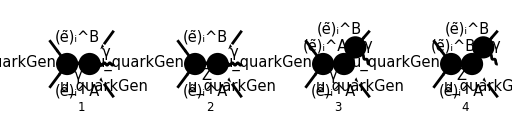

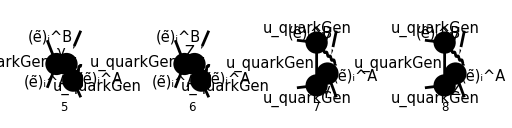

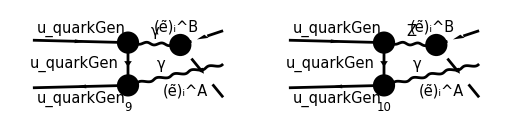

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

## Quark amplitudes

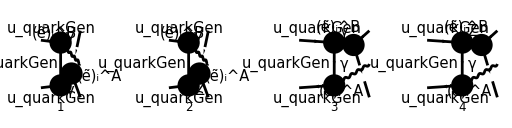

```mathematica
diagsQuark[0]=DiagramExtract[diags[0],{7,8,9,10}];
Paint[
diagsQuark[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MrqList[0]=FCFAConvert[
CreateFeynAmp[diagsQuark[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{MQU[quarkGen]->0};
```

```mathematica
Mrqγ[0]=(MrqList[0][[{1,3}]]//Total)(3/2SMP["e_Q"])^2;
MrqZ[0]=(MrqList[0][[{2,4}]]//Total//ZSimplify)3/2SMP["e_Q"];
```

```mathematica
Mrq[0]=Mrqγ[0]+MrqZ[0];
Mrq[1]=Mrq[0]//ReplaceAll[#,{
p2-k1-k2->k-p1,
k1+k2-p2->p1-k
}]&;
Mrq[2]=Mrq[1]//FeynAmpDenominatorExplicit//DiracSimplify//FullSimplify
```

(e^3 e_Q (2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)) (k·p_1) Q^2+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)) (k·p_1) Q^2+2 Z_l_i^AB (-Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)) (k·p_1)-Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)) (k·p_1)+2 (-Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_2·ε^*(k)) (k·p_1)+(k·p_2) (-Z_q_R (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+2 (Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))-Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_1·ε^*(k)))) Q^2-IndexDelta(A,B) ((k·p_2) (-(φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(φ(p_1))+(φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(φ(p_1))+2 ((φ(-p_2)).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1))) (p_1·ε^*(k)))+(k·p_1) ((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1))+2 ((φ(-p_2)).(γ·k_2).(φ(p_1))-(φ(-p_2)).(γ·k_1).(φ(p_1))) (p_2·ε^*(k)))) (cos(θ_W))^2 e_Q (Q-m_Z) (Q+m_Z) (sin(θ_W))^2) δ_Col1Col2)/(2 Q^2 (k·p_1) (k·p_2) (cos(θ_W))^2 (Q^2-m_Z^2) (sin(θ_W))^2)

### Hand calculation

```mathematica
MrqHand[0]=-1/2SMP["e"]^3SMP["e_Q"]SUNFDelta[Col1,Col2]FVD[k1-k2,μ]FVD[Polarization[k,-I],ν](SMP["e_Q"]IndexDelta[A,B]/Q^2 SpinorVBarD[p2].Stensor[μ,ν].SpinorUD[p1]-ZliAB/(SMP["sin_W"]^2SMP["cos_W"]^2(Q^2-SMP["m_Z"]^2))SpinorVBarD[p2].Stensor[μ,ν].G5lr.SpinorUD[p1]);
MrqHand[1]=MrqHand[0]//Contract//FeynAmpDenominatorExplicit//DiracSimplify//FullSimplify
```

(e^3 e_Q (2 Z_l_i^AB Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)) (k·p_1) Q^2+2 Z_l_i^AB Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1)) (k·p_1) Q^2+2 Z_l_i^AB (-Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^6.(φ(p_1)) (k·p_1)-Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(γ̄)^7.(φ(p_1)) (k·p_1)+2 (-Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_2·ε^*(k)) (k·p_1)+(k·p_2) (-Z_q_R (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+2 (Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))+Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))-Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1))-Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))) (p_1·ε^*(k)))) Q^2-IndexDelta(A,B) ((k·p_2) (-(φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(φ(p_1))+(φ(-p_2)).(γ·k_2).(γ·k).(γ·ε^*(k)).(φ(p_1))+2 ((φ(-p_2)).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·k_2).(φ(p_1))) (p_1·ε^*(k)))+(k·p_1) ((φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_2).(φ(p_1))+2 ((φ(-p_2)).(γ·k_2).(φ(p_1))-(φ(-p_2)).(γ·k_1).(φ(p_1))) (p_2·ε^*(k)))) (cos(θ_W))^2 e_Q (Q-m_Z) (Q+m_Z) (sin(θ_W))^2) δ_Col1Col2)/(2 Q^2 (k·p_1) (k·p_2) (cos(θ_W))^2 (Q^2-m_Z^2) (sin(θ_W))^2)

```mathematica
FCCompareResults[Mrq[2],MrqHand[1]];
```

Check of the results: The results agree.

## Slepton amplitude

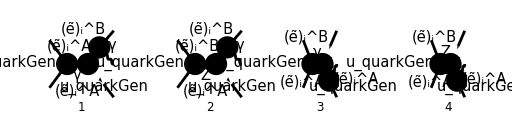

```mathematica
diagsSlepton[0]=DiagramExtract[diags[0],{3,4,5,6}];
Paint[
diagsSlepton[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
MrlList[0]=FCFAConvert[
CreateFeynAmp[diagsSlepton[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->True,
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{
MQU[quarkGen]->0,
MSf[B,2,i]->m1,
MSf[A,2,i]->m2
};
```

```mathematica
Mrlγ[0]=(MrlList[0][[{1,3}]]//Total//FCE//ReplaceAll[#,{
FAD[{-k-k1,m2}]->FAD[{k+k1,m1}]
}]&)3/2SMP["e_Q"]
MrlZ[0]=MrlList[0][[{2,4}]]//Total//ZSimplify
```

3/2 e_Q (-(2 e^3 δ_Col1Col2 (-(k·ε^*(k))-2 (k_1·ε^*(k))) IndexDelta(A,B) (φ(-p_2)).(γ·(k+k_1-k_2)).(φ(p_1)))/(3 (k+k_1+k_2)^2 ((k+k_1)^2-m_1^2))-(2 e^3 δ_Col1Col2 (-(k·ε^*(k))-2 (k_2·ε^*(k))) IndexDelta(A,B) (φ(-p_2)).(γ·(k-k_1+k_2)).(φ(p_1)))/(3 (k+k_1+k_2)^2 ((k+k_2)^2-m_2^2)))

(ⅈ e^2 Z_l_i^AB (((k·ε^*(k)+2 (k_1·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(k+k_1-k_2)).(γ̄)^7+Z_q_R (γ·(k+k_1-k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((-k-k_1)^2-m_1^2)+((k·ε^*(k)+2 (k_2·ε^*(k))) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·(k-k_1+k_2)).(γ̄)^7+Z_q_R (γ·(k-k_1+k_2)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((k+k_2)^2-m_2^2)))/((cos(θ_W)) (sin(θ_W)) ((k+k_1+k_2)^2-m_Z^2))

```mathematica
Mrl[0]=Mrlγ[0]+MrlZ[0];
Mrl[1]=Mrl[0]//ReplaceAll[#,{
k+k1+k2->p1+p2,
k+k1-k2->p1+p2-2k2,
k-k1+k2->p1+p2-2k1
}]&;
Mrl[2]=Mrl[1]//FeynAmpDenominatorExplicit//DiracSimplify//FCE//ReplaceAll[#,SPD[k,Polarization[k,-I]]->0]&//FullSimplify
```

(2 e^3 δ_Col1Col2 ((k·k_2) (k_1·ε^*(k)) (2 s Z_l_i^AB (Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))+e_Q (cos(θ_W))^2 (m_Z^2-s) (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·k_2).(φ(p_1)))+(k·k_1) (k_2·ε^*(k)) (2 s Z_l_i^AB (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))+e_Q (cos(θ_W))^2 (m_Z^2-s) (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)))))/(s (k·k_1) (k·k_2) (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2)

### Hand calculation

```mathematica
MrlHand[0]=-2SMP["e"]^3SUNFDelta[Col1,Col2]FVD[Polarization[k,-I],ν]Ttensor[μ,ν](SMP["e_Q"]IndexDelta[A,B]/s SpinorVBarD[p2].GAD[μ].SpinorUD[p1]-ZliAB/(SMP["sin_W"]^2SMP["cos_W"]^2(s-SMP["m_Z"]^2))SpinorVBarD[p2].GAD[μ].G5lr.SpinorUD[p1])
MrlHand[1]=MrlHand[0]//Contract//FeynAmpDenominatorExplicit//DiracSimplify//FullSimplify
```

-2 e^3 δ_Col1Col2 (ε^*)^ν(k) ((k_2^μ k_1^ν)/(k·k_1)+(k_1^μ k_2^ν)/(k·k_2)) ((e_Q IndexDelta(A,B) v̄(p_2).γ^μ.u(p_1))/s-(Z_l_i^AB v̄(p_2).γ^μ.((1-(γ̄)^5) Z_q_L+((γ̄)^5+1) Z_q_R).u(p_1))/((cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2))

(2 e^3 δ_Col1Col2 (2 s Z_l_i^AB ((k·k_2) (k_1·ε^*(k)) (Z_q_L (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))+(k·k_1) (k_2·ε^*(k)) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1))))-e_Q (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2 IndexDelta(A,B) ((k·k_2) (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(φ(p_1))+(k·k_1) (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(φ(p_1)))))/(s (k·k_1) (k·k_2) (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2)

```mathematica
FCCompareResults[Mrl[2],MrlHand[1]];
```

Check of the results: The results agree.

## 4-vertex amplitude

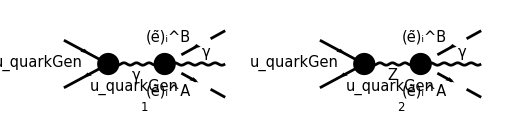

```mathematica
diags4[0]=DiagramExtract[diags[0],{1,2}];
Paint[
diags4[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

```mathematica
Mr4List[0]=FCFAConvert[
CreateFeynAmp[diags4[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->True,
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{
MQU[quarkGen]->0,
MSf[B,2,i]->m1,
MSf[A,2,i]->m2
}
```

{-(4 e^3 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))/(3 (k+k_1+k_2)^2),(ⅈ e^2 (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-p_2)).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ·ε^*(k)).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ·ε^*(k)).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k+k_1+k_2)^2-m_Z^2))}

```mathematica
Mr4γ[0]=Mr4List[0][[1]]3/2SMP["e_Q"]
Mr4Z[0]=Mr4List[0][[2]]//ZSimplify
```

-(2 e^3 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)))/(k+k_1+k_2)^2

-(2 ⅈ e^2 Z_l_i^AB (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Z_q_L (γ·ε^*(k)).(γ̄)^7+Z_q_R (γ·ε^*(k)).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k+k_1+k_2)^2-m_Z^2))

```mathematica
Mr4[0]=Mr4γ[0]+Mr4Z[0];
Mr4[1]=Mr4[0]//ReplaceAll[#,{
k+k1+k2->p1+p2
}]&;
Mr4[2]=Mr4[1]//FeynAmpDenominatorExplicit//DiracSimplify//FullSimplify
```

(2 e^3 δ_Col1Col2 (2 s Z_l_i^AB (Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))+e_Q (cos(θ_W))^2 (m_Z^2-s) (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(φ(p_1))))/(s (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2)

### Hand calculation

```mathematica
Mr4Hand[0]=-2SMP["e"]^3SUNFDelta[Col1,Col2] FVD[Polarization[k,-I],μ](SMP["e_Q"]IndexDelta[A,B]/s SpinorVBarD[p2].GAD[μ].SpinorUD[p1]-ZliAB/(SMP["sin_W"]^2SMP["cos_W"]^2(s-SMP["m_Z"]^2))SpinorVBarD[p2].GAD[μ].G5lr.SpinorUD[p1]);
Mr4Hand[1]=Mr4Hand[0]//Contract//FeynAmpDenominatorExplicit//DiracSimplify//FullSimplify
```

(2 e^3 δ_Col1Col2 (2 s Z_l_i^AB (Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))+e_Q (cos(θ_W))^2 (m_Z^2-s) (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(φ(p_1))))/(s (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2)

```mathematica
FCCompareResults[Mr4[2],Mr4Hand[1]];
```

Check of the results: The results agree.

## Simplifying phase space integrand (quark--slepton interference)

```mathematica
FCClearScalarProducts[];
SPD[p1] = SPD[p2] = SPD[k] = 0;
SPD[k1] = m1^2;
SPD[k2] = m2^2;
SPD[p1, p2] = s/2;
```

```mathematica
top1ki[expr_]:=ReplaceAll[FCE[expr],{
SPD[p2,k1]->m1^2+SPD[k1,k2]+SPD[k1,k]-SPD[p1,k1],
SPD[p2,k2]->m2^2+SPD[k1,k2]+SPD[k2,k]-SPD[p1,k2]
}];
pikikToxyz[expr_]:=ReplaceAll[expr,{
SPD[p1,k]->s/2Z Y,
SPD[p2,k]->s/2Z y,
SPD[k1,k]->s/4Z (1-x),
SPD[k2,k]->s/4Z (1+x)
}];
p1kiToyzPhi[expr_]:=ReplaceAll[expr,{
SPD[p1,k1]->s/4(y+z Y+Φ),
SPD[p1,k2]->s/4(y+z Y-Φ)
}];
```

```mathematica
yzToYZ[expr_]:=ReplaceAll[expr,{
1-z->Z,
z-1->-Z,
1-y->Y,
y-1->-Y
}];
YZToyz[expr_]:=ReplaceAll[expr,{
Z->1-z,
Y->1-y
}];
xyzSimplify[expr_]:=ReplaceAll[expr,{
y+Y->1,
z+Z->1,
-z+Z+1->2Z,
1-z->Z,
z-1->-Z,
1-Z->z,
Z-1->-z,
1-y->Y,
y-1->-Y,
1-Y->y,
Y-1->-y
}];
ABToxyz[expr_]:=ReplaceAll[expr,{
B->z Y(x+2(mt1^2-mt2^2))-x y,
A->2Sqrt[y]Sqrt[Y]Sqrt[z]Sqrt[Xp Xm]
}];
```

Note the use of  Y=(1-y), Z=(1-z), and Xp=(xp-x), Xm=(x-xm) to simplify expressions while keeping these structures.

```mathematica
pikjCollect={SPD[p1,k1],SPD[p1,k2],SPD[p2,k1],SPD[p2,k2]};
kCollect={SPD[p1,k],SPD[p2,k],SPD[k1,k],SPD[k2,k]};
```

exprFirst[0] means only the first term, before adding the (p1<->p2) and (k1<->k2) parts.
The expression given here was arrived at by hand, with the help of Mathematica

```mathematica
exprFirst[0]=2(2SPD[p1,k1]/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k1,p1,k2]]+m1^2/(SPD[p1,k]SPD[k1,k])DiracTrace[GSD[p2,k,p1,k2]])
exprFirst[1]=exprFirst[0]//DiracSimplify//FullSimplify
```

2 ((m_1^2 tr((γ·p_2).(γ·k).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1))+(2 (k_1·p_1) tr((γ·p_2).(γ·k_1).(γ·p_1).(γ·k_2)))/((k·k_1) (k·p_1)))

1/((k·k_1) (k·p_1))(8 (k_2·p_2) (2 (k_1·p_1)^2+m_1^2 (k·p_1))+8 (k_2·p_1) (m_1^2 (k·p_2)+2 (k_1·p_1) (k_1·p_2))-4 m_1^2 s (k·k_2)-8 s (k_1·k_2) (k_1·p_1))

```mathematica
exprFirstNum[0]=(exprFirst[1]//Numerator)/8
exprFirstDen[0]=(exprFirst[1]//Denominator)/8
```

1/8 (8 (k_2·p_2) (2 (k_1·p_1)^2+m_1^2 (k·p_1))+8 (k_2·p_1) (m_1^2 (k·p_2)+2 (k_1·p_1) (k_1·p_2))-4 m_1^2 s (k·k_2)-8 s (k_1·k_2) (k_1·p_1))

1/8 (k·k_1) (k·p_1)

```mathematica
exprFirstNum[1]=exprFirstNum[0]//FCE//Collect2[#,pikjCollect,Factoring->FullSimplify]&
```

m_1^2 (k·p_2) (k_2·p_1)+m_1^2 (k·p_1) (k_2·p_2)-1/2 m_1^2 s (k·k_2)-s (k_1·k_2) (k_1·p_1)+2 (k_1·p_1) (k_1·p_2) (k_2·p_1)+2 (k_1·p_1)^2 (k_2·p_2)

```mathematica
exprFirstNum[2]=exprFirstNum[1]SPD[p2,k]SPD[k2,k]
exprDen[0]=exprFirstDen[0]SPD[p2,k]SPD[k2,k]
```

(k·k_2) (k·p_2) (m_1^2 (k·p_2) (k_2·p_1)+m_1^2 (k·p_1) (k_2·p_2)-1/2 m_1^2 s (k·k_2)-s (k_1·k_2) (k_1·p_1)+2 (k_1·p_1) (k_1·p_2) (k_2·p_1)+2 (k_1·p_1)^2 (k_2·p_2))

1/8 (k·k_1) (k·k_2) (k·p_1) (k·p_2)

Full expression found by hand, starting from exprFirstNum[1] and adding (p1<->p2) and (k1<->k2) parts, and using the symmetries under these exchanges in some of the factors.

```mathematica
exprNum[0]=2(SPD[p2,k]SPD[k2,k]SPD[p1,k1]-SPD[p1,k]SPD[k2,k]SPD[p2,k1]-SPD[p2,k]SPD[k1,k]SPD[p1,k2]+SPD[p1,k]SPD[k1,k]SPD[p2,k2])(SPD[p1,k1]SPD[p2,k2]+SPD[p1,k2]SPD[p2,k1]-s/2 SPD[k1,k2])+(SPD[p2,k]-SPD[p1,k])(m1^2SPD[k2,k](SPD[p2,k]SPD[p1,k2]+SPD[p1,k]SPD[p2,k2]-s/2 SPD[k2,k])-m2^2SPD[k1,k](SPD[p2,k]SPD[p1,k1]+SPD[p1,k]SPD[p2,k1]-s/2 SPD[k1,k]))
```

(k·p_2-k·p_1) (m_1^2 (k·k_2) ((k·p_2) (k_2·p_1)+(k·p_1) (k_2·p_2)-1/2 s (k·k_2))-m_2^2 (k·k_1) ((k·p_2) (k_1·p_1)+(k·p_1) (k_1·p_2)-1/2 s (k·k_1)))+2 ((k·k_2) (k·p_2) (k_1·p_1)-(k·k_2) (k·p_1) (k_1·p_2)-(k·k_1) (k·p_2) (k_2·p_1)+(k·k_1) (k·p_1) (k_2·p_2)) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)-1/2 s (k_1·k_2))

```mathematica
FCCompareResults[exprNum[0],
exprFirstNum[2]
-(exprFirstNum[2]//ReplaceAll[#,{p1->p2,p2->p1}]&)
-(exprFirstNum[2]//ReplaceAll[#,{k1->k2,k2->k1,m1->m2,m2->m1}]&)
+(exprFirstNum[2]//ReplaceAll[#,{p1->p2,p2->p1,k1->k2,k2->k1,m1->m2,m2->m1}]&)
];
```

Check of the results: The results agree.

Reducing to only p1.k1 and p1.k2, and inserting expressions for pi.k and ki.k.

```mathematica
exprNum[1]=exprNum[0]//top1ki//FullSimplify//pikikToxyz//FCE//ReplaceAll[#,{
SPD[k1,k2]->(s z-m1^2-m2^2)/2
}]&//FullSimplify//FRH//p1kiToyzPhi//FullSimplify//ReplaceAll[#,{
m1->Sqrt[s z] mt1,
m2->Sqrt[s z] mt2
}]&//FullSimplify//xyzSimplify//Collect2[#,Φ,Factoring->FullSimplify,IsolateNames->KK]&
```

1/64 KK(470) Φ^3+1/64 KK(492) Φ^2-1/64 KK(488) Φ+(KK(506))/64

All coefficients have a common factor s^5(1-z)^2. We can factor this out.

```mathematica
exprNum[2]=64/(s^5 Z^2)exprNum[1]//FRH//FullSimplify//Collect2[#,Φ,Factoring->FullSimplify,IsolateNames->KK]&
exprDen[1]=64/(s^5 Z^2)exprDen[0]//FCE//pikikToxyz
```

KK(491) Φ^2+KK(507) Φ+KK(505)+Φ^3

((1-x) (x+1) y Y Z^2)/(8 s)

```mathematica
c2=KK[491]//FRH//xyzSimplify//yzToYZ//ReplaceAll[#,Z->1-z]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
c1=KK[507]//FRH//xyzSimplify//yzToYZ//ReplaceAll[#,Z->1-z]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
c0=KK[505]//FRH//xyzSimplify//yzToYZ//ReplaceAll[#,Z->1-z]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&
```

-KK(508) Y+KK(509)+x y

KK(522) y^2+2 KK(515) y Y+KK(520) y+KK(513) Y^2+KK(518) Y+2 KK(523)

KK(561) y^3+KK(546) y^2 Y+KK(548) y^2+KK(541) y Y^2+KK(536) y Y+KK(565) y+KK(528) Y^3+KK(553) Y^2+KK(560) Y

### Doing the Φ integrals

```mathematica
int[n_]:=Φ^n (Φp-Φ)^((d-5)/2)(Φ-Φm)^((d-5)/2);
```

```mathematica
Integrate[int[0],{Φ,Φm,Φp}]
Integrate[int[1],{Φ,Φm,Φp}]
Integrate[int[2],{Φ,Φm,Φp}]
Integrate[int[3],{Φ,Φm,Φp}]
```

(π^(3/2) 2^(4-d) (Φ^+-Φ^-)^(d-4) sec((π d)/2))/(5/2-d/2 d/2-1)

(√π 2^(3-d) (Φ^-+Φ^+) (Φ^+-Φ^-)^(d-4) (d-3)/2)/(d/2-1)

(√π 2^(2-d) (Φ^+-Φ^-)^(d-4) ((d-1) (Φ^-)^2+(d-1) (Φ^+)^2+2 (d-3) Φ^+ Φ^-) (d-1)/2)/((d-3) d/2)

(√π 2^-d (Φ^-+Φ^+) (Φ^+-Φ^-)^(d-4) ((d+1) (Φ^-)^2+(d+1) (Φ^+)^2+2 (d-5) Φ^+ Φ^-) (d-3)/2)/(d/2)

We can show (done by hand) that these integrals are all proportional to the first one, such that (with ) we have

## Doing the y integral

After some simplifications, the y integral in the full cross section is (using d2=d-2)

```mathematica
yint[0]=Hold[y^((d-6)/2)Y^((d-6)/2)(B^3+c2 B^2+c1 B+c0+(c2+3B)/d2 A^2)]
```

Hold[y^((d-6)/2) Y^((d-6)/2) ((A^2 (3 B+c_2))/d2+B^3+B^2 c_2+B c_1+c_0)]

```mathematica
Hold[B^3+c2 B^2+c1 B+c0+(c2+3B)/d2 A^2]
%//FRH//ABToxyz//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&;
%//ReplaceAll[#,{
y^3->y^2(1-Y),
Y^3->Y^2(1-y)
}]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&;
(%//ReplaceAll[#,{
y^2->y(1-Y),
Y^2->Y(1-y)
}]&//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&);
(%/(y Y)//Collect2[#,{y,Y},Factoring->FullSimplify,IsolateNames->KK]&);
(* Note: Divided by (yY), so we multiply by (yY)^((d-4)/2) instead of (yY)^((d-6)/2) in the end*)
yint[1]=(%//SelectNotFree2[#,{y,Y}]&)+(%//SelectFree2[#,{y,Y}]&)(y+Y)//FRH//Collect2[#,{y,Y,d2},Factoring->FullSimplify,IsolateNames->KK]&;
yint[1]=% y^((d-4)/2)Y^((d-4)/2)//ReplaceAll[#,Y->1-y]&
yint[2]=Integrate[%,{y,0,1}]//FullSimplify
```

Hold[(A^2 (3 B+c_2))/d2+B^3+B^2 c_2+B c_1+c_0]

(1-y)^((d-4)/2) y^((d-4)/2) ((4 KK(668) (1-y))/d2-(4 KK(668) y)/d2-2 KK(673) (1-y)+2 KK(673) y)

0